There is nothing wrong with doing the wave equation but you only need to do the eigenvalue problem for the Laplacian

```mathematica
Clear[α,U,u,k]
hmm=DSolveValue[U''[u]+(u^2 k^2-α)U[u]==0,U[u],u]
```

C[2] ParabolicCylinderD[(-k-ⅈ α)/(2 k),(-1)^(3/4) √2 √k u]+C[1] ParabolicCylinderD[(-k+ⅈ α)/(2 k),(-1)^(1/4) √2 √k u]

I grabbed to two pieces from the solution above.  As you can see both of them are genuinely complex.

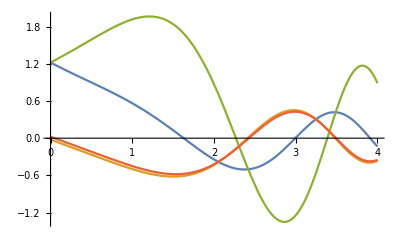

```mathematica
U1[k_,α_][u_]:=ParabolicCylinderD[(-k+ⅈ α)/(2 k),(-1)^(1/4) √2 √k u]
U2[k_,α_][u_]:=ParabolicCylinderD[(-k-ⅈ α)/(2 k),(-1)^(3/4) √2 √k u]

Plot[{
Re[U1[1,0.2][u]],
Im[U1[1,0.2][u]],
Re[U2[1,0.2][u]],
Im[U2[1,0.2][u]]
},{u,0, 4}]
```

If I solve a system (with any values of k and α) with real values on the RHS I should get a real valued solution albeit with complex coefficients giving those real values.  See below for an example.

```mathematica
Clear[k,α]
k=1.2; α =9.6;
Sub=Solve[{
c1 U1[k,α][0]+c2 U2[k,α][0]==1.2,
c1 U1[k,α][1]+c2 U2[k,α][1]==2.3
}]
f[u_]=c1 U1[k,α][u]+c2 U2[k,α][u]/.Sub
TabView[{
"re"->Plot[f[u],{u,0,1}],
"im"->Plot[Im[f[u]],{u,0,1}]}]
```

{{c1→0.0367465-0.0868456 ⅈ,c2→0.00358558+0.00847448 ⅈ}}

{(0.00358558+0.00847448 ⅈ) ParabolicCylinderD[-0.5-4. ⅈ,(-1.09545+1.09545 ⅈ) u]+(0.0367465-0.0868456 ⅈ) ParabolicCylinderD[-0.5+4. ⅈ,(1.09545+1.09545 ⅈ) u]}

12

Of course, you want to solve for the values of the parameters at which the determinant of the system is equal to zero so that you have non-trivial solutions to the linear system with zeros on the right hand side. I am going to pretend I already know k=2 and just work on α.  With the right numbers the αs you compute should produce a numerically zero value for the imaginary part of the final answer.

```mathematica
Clear[F,α,k]
k=2;
F[α_]:= Det[({{U1[k,α][0], U2[k,α][0]}, {U1[k,α][0], U2[k,α][1]}})]
FindRoot[F[α]==0,{α,1.2}]
```

{α→-0.111154+0.797852 ⅈ}